```mathematica
(*(*Clear all previous definitions to ensure a clean run*)ClearAll["Global`*"];*)

(*************************************************************************)
(*STEP 1:DEFINE THE "GROUND TRUTH" FUNCTION (UNCHANGED)*)
(*************************************************************************)

mfptSingleIntegral[b_?NumericQ]:=Module[{integrand,result},integrand[x_]:=Exp[-x^2/2]*(E^((x/Sqrt[2])^2) Erfc[-x/Sqrt[2]])^2;
result=NIntegrate[integrand[x],{x,-Infinity,b},WorkingPrecision->25];
(Sqrt[Pi]/(2*Sqrt[2]))*result];
mfptAnalytic[b_]:=Module[{integrand,result},integrand[x_]:=Exp[-x^2/2]*(E^((x/Sqrt[2])^2) Erfc[-x/Sqrt[2]])^2;
result=Integrate[integrand[x],{x,-Infinity,b}];
(Sqrt[Pi]/(2*Sqrt[2]))*result];
```

```mathematica
(*************************************************************************)
(*STEP 2:GENERATE OR LOAD PRE-COMPUTED DATA*)
(*************************************************************************)

(*---Parameters to adjust---*)
bMin=-6.0;
bMax=10.0; 
numPoints=4000;
SetDirectory[NotebookDirectory[]]
dataFilename="mfpt_lookup_data.mx";

(*---Check for data file,then load or generate as needed---*)
If[FileExistsQ[dataFilename],(*If file exists,load it instantly*)Print["Loading pre-computed data from \"",dataFilename,"\"..."];
{bValues,tValues}=Import[dataFilename,"MX"];,(*If file doesn't exist,run the one-time generation and save it*)Print["No data file found. Generating new data... (this may take a moment)"];
bValues=Range[bMin,bMax,(bMax-bMin)/(numPoints-1)];
tValues=Monitor[Table[mfptSingleIntegral[b],{b,bValues}],StringForm["Calculating for b = ``",N[b,4]]];
Export[dataFilename,{bValues,tValues},"MX"];
Print["Data generation complete. Saved to \"",dataFilename,"\" for future sessions."];];


(*************************************************************************)
(*STEP 3:CREATE THE FAST HYBRID FUNCTION (UNCHANGED)*)
(*************************************************************************)

splineFunction=Interpolation[Transpose[{bValues,tValues}]];
asymptoticFormula[b_]:=(Sqrt[2*Pi]/b)*Exp[b^2/2];
mfptLowerTail[b_?NumericQ]=Assuming[b<1,(Sqrt[Pi]/(2*Sqrt[2]))*Integrate[Exp[x^2/2](Series[Erfc[-x/Sqrt[2]],{x,-Infinity,5}]//Normal)^2,{x,-Infinity,b}]]//FullSimplify;
fastMFPT[b_?NumericQ]:=Which[b<bMin,mfptLowerTail[b],b>bMax,asymptoticFormula[b],True,splineFunction[b]];
fastMFPT[b_List]:=fastMFPT/@b;


(*************************************************************************)
(*STEP 4:WIDE-RANGE ACCURACY TEST (UNCHANGED)*)
(*************************************************************************)

testPoints=Table[RandomReal[{i,i+1}],{i,-12,12}];
Print[Style["\n--- Wide-Range Accuracy Test (for small b I trust the asymptotics, not the -Exact Value-) ---",Bold,14]];
results=Monitor[Table[Module[{valExact,valApprox,absError,relError},valExact=mfptSingleIntegral[b];
valApprox=fastMFPT[b];
absError=Abs[valExact-valApprox];
relError=If[valExact!=0,absError/valExact,0];
{b,valExact,valApprox,absError,relError}],{b,testPoints}],StringForm["Testing b = ``",N[b,4]]];
tableData=Prepend[results,Item[#,BaseStyle->{"Bold"}]&/@{"b","Exact Value","Approx Value","Abs. Error","Rel. Error"}];
Print[Grid[tableData,Frame->All,Spacings->{2,1},Alignment->{{Left,".",".",".","."}},Background->{None,{Lighter[Gray,.9],{White,Lighter[Blend[{Blue,Green}],.9]}}}]];
```

/Users/btw970/lin_alg/ambition/The-Lotka-Volterra-Metacommunity-Model/Infinite_pool_assembly

No data file found. Generating new data... (this may take a moment)

Data generation complete. Saved to "mfpt_lookup_data.mx" for future sessions.

--- Wide-Range Accuracy Test (for small b I trust the asymptotics, not the -Exact Value-) ---

b | Exact Value | Approx Value | Abs. Error | Rel. Error
-11.9983 | 1.225851738026947458624982×10^-35 | 4.00094×10^-33 | 3.98868×10^-33 | 325.381
-10.8337 | 9.825979528753906396784947×10^-30 | 2.63192×10^-27 | 2.62209×10^-27 | 266.853
-9.61172 | 3.70453256278122450726335×10^-24 | 7.88509×10^-22 | 7.84804×10^-22 | 211.85
-8.87392 | 4.272477640519499774259646×10^-21 | 7.81065×10^-19 | 7.76793×10^-19 | 181.813
-7.35466 | 1.651686786291066120113592×10^-15 | 1.66531×10^-15 | 1.36214×10^-17 | 0.00824695
-6.70794 | 2.021406754817610708417835×10^-13 | 2.02226×10^-13 | 8.48805×10^-17 | 0.000419908
-5.36717 | 1.22828260394163797161128×10^-9 | 1.22828×10^-9 | 3.94245×10^-18 | 3.20972×10^-9
-4.7137 | 4.693737277818735294472421×10^-8 | 4.69374×10^-8 | 1.76985×10^-16 | 3.77067×10^-9
-3.60241 | 9.5390954234260955825189×10^-6 | 9.5391×10^-6 | 1.02856×10^-14 | 1.07825×10^-9
-2.84195 | 0.0001955577847201395086503357 | 0.000195558 | 1.15726×10^-13 | 5.91775×10^-10
-1.37638 | 0.01801013684436879772281989 | 0.0180101 | 1.96202×10^-12 | 1.0894×10^-10
-0.73894 | 0.08061962856258109067033921 | 0.0806196 | 9.3664×10^-13 | 1.1618×10^-11
0.98469 | 1.795420503157786246661245 | 1.79542 | 7.33278×10^-11 | 4.08416×10^-11
1.92259 | 8.42896413510616998231793 | 8.42896 | 6.03833×10^-10 | 7.16379×10^-11
2.83351 | 56.25581630488076979382527 | 56.2558 | 1.42614×10^-8 | 2.5351×10^-10
3.49582 | 358.368069413364208496639 | 358.368 | 3.30457×10^-7 | 9.22116×10^-10
4.72689 | 39690.77438462825163671846 | 39690.8 | 0.0000229164 | 5.77374×10^-10
5.92242 | 1.804911775705899562998645×10^7 | 1.80491×10^7 | 0.0637486 | 3.53195×10^-9
6.94088 | 1.067736793753867208884964×10^10 | 1.06774×10^10 | 149.629 | 1.40137×10^-8
7.60213 | 1.189800241817041283065706×10^12 | 1.1898×10^12 | 20988.1 | 1.76401×10^-8
8.37139 | 5.01679524666915546283699×10^14 | 5.0168×10^14 | 2.69272×10^6 | 5.36741×10^-9
9.14014 | 3.840979372620666768121537×10^17 | 3.84098×10^17 | 4.96159×10^9 | 1.29175×10^-8
10.5482 | 3.472917554589279938147687×10^23 | 3.44112×10^23 | 3.18013×10^21 | 0.00915693
11.1682 | 2.749943696310330321486189×10^26 | 2.72753×10^26 | 2.24159×10^24 | 0.00815139
12.9789 | 7.364932157804665737965421×10^35 | 7.32068×10^35 | 4.42567×10^33 | 0.00600911

```mathematica
(************************************************************************)
```

(I found this rule because Mathematica gave me different formulae when rho -> 1 and for arbitrary rho . The requirement that they are equal for rho == 0 led to this Rule (of which Mathematica seems unaware).
Because this 2F2 converges to zero for negative arguments, It's actually better to use the negative argument form for numerical integration!

```mathematica
Rule2F2=HypergeometricPFQ[{1,1},{3/2,2},s_]:>(π Erf[√s] Erfi[√s])/(2 s)-HypergeometricPFQ[{1,1},{3/2,2},-s]
```

HypergeometricPFQ[{1,1},{3/2,2},s_]:>(π Erf[√s] Erfi[√s])/(2 s)-HypergeometricPFQ[{1,1},{3/2,2},-s]

```mathematica
Series[HypergeometricPFQ[{1,1},{3/2,2},s],{s,0,10}]
Series[HypergeometricPFQ[{1,1},{3/2,2},s]/.Rule2F2,{s,0,10}]
```

1+s/3+(4 s^2)/45+(2 s^3)/105+(16 s^4)/4725+(16 s^5)/31185+(64 s^6)/945945+(16 s^7)/2027025+(256 s^8)/310134825+(256 s^9)/3273645375+(1024 s^10)/151242416325+O[s]^11

1+s/3+(4 s^2)/45+(2 s^3)/105+(16 s^4)/4725+(16 s^5)/31185+(64 s^6)/945945+(16 s^7)/2027025+(256 s^8)/310134825+(256 s^9)/3273645375+(1024 s^10)/151242416325+O[s]^(21/2)

```mathematica
coefficient1=Assuming[n>=-2,SeriesCoefficient[(π Erf[x] Erfi[x])/(2 x^2)-HypergeometricPFQ[{1,1},{3/2,2},-x^2],{x,0,n}]//FullSimplify]
coefficient2=
Assuming[n>=-2,SeriesCoefficient[HypergeometricPFQ[{1,1},{3/2,2},x^2],{x,0,n}]//FullSimplify]

(* Should be possible to proove equality of these by demonstrating that coefficient2 satisfies the recursion equations in coefficient1 *)
```

Piecewise[{{1/2 π [2+n], n<0||Mod[n,2]>0}, {-(ⅈ^n √π)/((2+n) Gamma[(3+n)/2])+1/2 π [2+n], True}}]

Piecewise[{{(√π)/((2+n) Gamma[(3+n)/2]), Mod[n,2]==0&&n≥0}, {0, True}}]

```mathematica
Assuming[Mod[n,2]==0&&n>=0,{coefficient1,coefficient2}//FullSimplify]
%//InputForm
```

{-(ⅈ^n √π)/((2+n) Gamma[(3+n)/2])+1/2 π [2+n],(√π)/((2+n) Gamma[(3+n)/2])}

{-((I^n*Sqrt[Pi])/((2 + n)*Gamma[(3 + n)/2])) + 
  (Pi*DifferenceRoot[Function[{y, n}, 
       {-4*n*y[n] + (1 + n)*(3 + n)*(4 + n)*y[4 + n] == 
         0, y[0] == 0, y[1] == 0, y[2] == 4/Pi, y[3] == 0}]][
     2 + n])/2, Sqrt[Pi]/((2 + n)*Gamma[(3 + n)/2])}

```mathematica
mu[X_]:=rho*(x0-X) (* with rho==1 Mathematica makes simpler results *)
(*mu[X_]:=-X*)a
sigma[X_]:=sig
```

a

```mathematica
V[X_]:=Piecewise[{{0,X>=Xb},{Infinity,X<Xb}}]
fM[X_]:=X
fM2[X_]:=X^2
fM2dt[X_]:=X*(X+mu[X]*dt)
fV[X_]:=1
```

```mathematica
eqs=mu[x]u'[x]+(1/2)sigma[x]^2D[u[x],{x,2}]+fM[x]==0&&u[0]==0
uMRule0=DSolve[eqs,u[x],x]//Last//FullSimplify
```

x+rho (-x+x0) u'[x]+1/2 sig^2 u''[x]==0&&u[0]==0

{u[x]→x/rho+(sig C[1] (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/(√rho)+1/sig^2 x0 (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
Series[u[x]/.uMRule0/.C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]x0/sig/Sqrt[rho]//FullSimplify,{x,Infinity,1}]//PowerExpand//Simplify
```

1/(2 rho)(-ⅈ ⅈ^(2 Floor[Arg[(2 x x0)/sig^2-x0^2/sig^2]/(2 π)]) π x0+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) (-(√π sig x0)/(√rho x)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) ((√π sig x0)/(√rho x)+O[1/x]^2)+(2 x+1/sig^2 x0 (ⅈ π sig^2+π sig^2 Erfi[(√rho x0)/sig]+2 rho x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]+sig^2 Log[rho]-2 sig^2 Log[sig]+2 sig^2 Log[x]-sig^2 PolyGamma[0,1/2])-(2 x0^2)/x+O[1/x]^2))

```mathematica
c1RuleM=C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]x0/sig/Sqrt[rho]
```

C[1]→(ⅇ^((rho x0^2)/sig^2) √π x0)/(√rho sig)

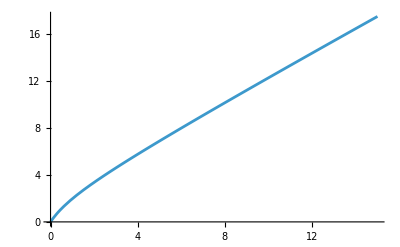

```mathematica
Plot[u[x]/.uMRule0/.c1RuleM/.rho->1/.sig->1/.x0->1/2//Evaluate,{x,0,15},WorkingPrecision->100]
```

```mathematica
uMRule=uMRule0/.c1RuleM//Simplify
```

{u[x]→x/rho+(ⅇ^((rho x0^2)/sig^2) √π x0 (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/rho+1/sig^2 x0 (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
eqs=mu[x]u'[x]+(1/2)sigma[x]^2D[u[x],{x,2}]+fV[x]==0&&u[0]==0
uVRule0=Assuming[rho>0&&sig>0&&x0>0,DSolve[eqs,u[x],x]//Last//FullSimplify]/.Rule2F2//FullSimplify
```

1+rho (-x+x0) u'[x]+1/2 sig^2 u''[x]==0&&u[0]==0

{u[x]→(sig C[1] (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/(√rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
Series[u[x]/.uVRule0/.C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]/sig/Sqrt[rho]//FullSimplify,{x,Infinity,1}]//PowerExpand//Simplify
```

1/(2 rho)(-ⅈ (-1)^Floor[Arg[(2 x x0)/sig^2-x0^2/sig^2]/(2 π)] π+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) (-(√π sig)/(√rho x)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) ((√π sig)/(√rho x)+O[1/x]^2)+(1/sig^2(ⅈ π sig^2+π sig^2 Erfi[(√rho x0)/sig]+2 rho x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]+sig^2 Log[rho]-2 sig^2 Log[sig]+2 sig^2 Log[x]-sig^2 PolyGamma[0,1/2])-(2 x0)/x+O[1/x]^2))

```mathematica
c1RuleV=C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]/sig/Sqrt[rho]
```

C[1]→(ⅇ^((rho x0^2)/sig^2) √π)/(√rho sig)

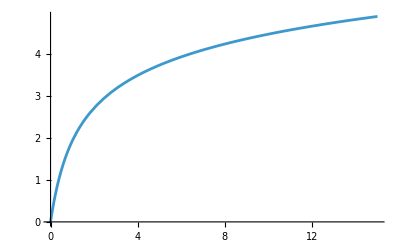

```mathematica
Plot[u[x]/.uVRule0/.c1RuleV/.rho->1/.sig->1/.x0->1/2//Evaluate,{x,0,15},WorkingPrecision->100]
```

```mathematica
uVRule=uVRule0/.c1RuleV//FullSimplify
```

{u[x]→(π (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
(* Compare this to mean first passage time function: *)

u[x]/.uVRule/.x0->0
Sqrt[Pi]*Integrate[Exp[x^2](1+Erf[x]),{x,0,b},GenerateConditions->False]//FunctionExpand//Expand
```

(π Erfi[(√rho x)/sig])/(2 rho)-(x^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x^2)/sig^2])/sig^2

1/2 π Erfi[b]+b^2 HypergeometricPFQ[{1,1},{3/2,2},b^2]

```mathematica
eqs=mu[x]u'[x]+(1/2)sigma[x]^2D[u[x],{x,2}]+fM2[x]==0&&u[0]==0
uM2Rule0=Assuming[rho>0&&sig>0&&x0>0,DSolve[eqs,u[x],x]//Last//FullSimplify]/.Rule2F2//FullSimplify
```

x^2+rho (-x+x0) u'[x]+1/2 sig^2 u''[x]==0&&u[0]==0

{u[x]→1/(2 rho)(x (x+2 x0)+2 ⅇ^((rho x (x-2 x0))/sig^2) √rho sig C[1] DawsonF[(√rho (x-x0))/sig]+2 √rho sig C[1] DawsonF[(√rho x0)/sig]+1/sig^2(sig^2+2 rho x0^2) (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]))}

```mathematica
Series[u[x]/.uM2Rule0/.C[1]->a*Sqrt[Pi]*Exp[rho x0^2/sig^2](sig^2+2 rho x0^2)/sig/Sqrt[rho]/(2rho),{x,Infinity,1}]//PowerExpand
```

ⅈ^(2 Floor[Arg[(2 x x0)/sig^2-x0^2/sig^2]/(2 π)]) (-(ⅈ a π sig^2)/(4 rho^2)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^2) ((a √π sig^3)/(4 rho^(5/2) x)+O[1/x]^2)+ⅈ^(2 Floor[Arg[(2 x x0)/sig^2-x0^2/sig^2]/(2 π)]) (-(ⅈ a π x0^2)/(2 rho)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^2) ((a √π sig x0^2)/(2 rho^(3/2) x)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) (-(√π sig (sig^2+2 rho x0^2))/(4 rho^(5/2) x)+O[1/x]^2)+(x^2/(2 rho)+(x0 x)/rho+1/(4 rho^2 sig^2)(sig^2+2 rho x0^2) (ⅈ π sig^2+2 a ⅇ^((rho x0^2)/sig^2) √π sig^2 DawsonF[(√rho x0)/sig]+2 rho x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]+sig^2 Log[rho]-2 sig^2 Log[sig]+2 sig^2 Log[x]-sig^2 PolyGamma[0,1/2])+(-sig^2 x0-2 rho x0^3)/(2 rho^2 x)+O[1/x]^2)

```mathematica
c1RuleM2=C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2](sig^2+2 rho x0^2)/sig/Sqrt[rho]/(2rho)
```

C[1]→(ⅇ^((rho x0^2)/sig^2) √π (sig^2+2 rho x0^2))/(2 rho^(3/2) sig)

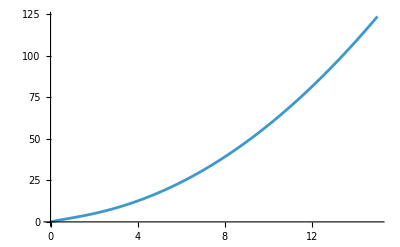

```mathematica
Plot[u[x]/.uM2Rule0/.c1RuleM2/.rho->1/.sig->1/.x0->1/2//Evaluate,{x,0,15},WorkingPrecision->100]
```

```mathematica
uM2Rule=uM2Rule0/.c1RuleM2//FullSimplify
```

{u[x]→1/(2 rho)(x (x+2 x0)+(π (sig^2+2 rho x0^2) (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(sig^2+2 rho x0^2) (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]))}

```mathematica
intV=integrate[(u[x]/.uVRule)*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]
intM=integrate[(u[x]/.uMRule)*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]
intM2=integrate[(u[x]/.uM2Rule)*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]
```

integrate[1/(√π sig)ⅇ^(-(rho (x-x0)^2)/sig^2) √rho ((π (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])),{x,0,∞}]

integrate[1/(√π sig)ⅇ^(-(rho (x-x0)^2)/sig^2) √rho (x/rho+(ⅇ^((rho x0^2)/sig^2) √π x0 (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/rho+1/sig^2 x0 (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])),{x,0,∞}]

integrate[1/(2 √π √rho sig)ⅇ^(-(rho (x-x0)^2)/sig^2) (x (x+2 x0)+(π (sig^2+2 rho x0^2) (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(sig^2+2 rho x0^2) (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])),{x,0,∞}]

```mathematica
simpleInt=PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x]*((π (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]))/.rho->1/.sig->1//FullSimplify
```

1/(√π)ⅇ^(-(x-x0)^2) (1/2 π (Erfi[x-x0]+Erfi[x0])-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(x-x0)^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},x0^2])

```mathematica
simpleIntegral[x0_]:=
fastMFPT[Sqrt[2]*x0]
```

```mathematica
simpleIntegral[0.0]-(Log[2]/2)
simpleIntegral[0]=Log[2]/2
(*WolframAlpha[ToString[%],IncludePods->"PossibleClosedForm"]*)
```

-1.11753×10^-11

Log[2]/2

```mathematica
simpleIntegral[c]//Timing
fastMFPT[Sqrt[2]*3]//Timing
mfptSingleIntegral[Sqrt[2]*3]//Timing
```

{0.000018,fastMFPT[√2 c]}

{0.000015,5117.26}

{0.019576,5117.259942826081699642779}

```mathematica
restoreRule={x0->x0*Sqrt[rho]/sig,x->x Sqrt[rho]/sig}
integrandRule=Solve[integrand==simpleInt/.HypergeometricPFQ[{1,1},{3/2,2},x0^2]->hyper/.restoreRule//Simplify,hyper]/.hyper->(HypergeometricPFQ[{1,1},{3/2,2},x0^2]/.restoreRule)//Last//FullSimplify
```

{x0→(√rho x0)/sig,x→(√rho x)/sig}

{HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]→1/(2 rho x0^2)(2 ⅇ^((rho (x-x0)^2)/sig^2) integrand √π sig^2-π sig^2 (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig])+2 rho (x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2])}

```mathematica
intVS=intV/.integrandRule//FullSimplify
intMS=intM/.integrandRule//FullSimplify
intM2S=intM2/.integrandRule//FullSimplify
```

integrate[integrand/(√rho sig),{x,0,∞}]

integrate[((ⅇ^(-(rho (x-x0)^2)/sig^2) x)/(√π)+integrand x0)/(√rho sig),{x,0,∞}]

integrate[((ⅇ^(-(rho (x-x0)^2)/sig^2) rho x (x+2 x0))/(√π)+integrand (sig^2+2 rho x0^2))/(2 rho^(3/2) sig),{x,0,∞}]

```mathematica
{intVS1,intMS1,intM2S1}=Assuming[rho>0&&sig>9,{intVS,intMS,intM2S}/.integrand->0/.integrate->Integrate]//FullSimplify
```

{0,((ⅇ^(-(rho x0^2)/sig^2) sig)/(√π)+√rho x0 (1+Erf[(√rho x0)/sig]))/(2 rho^(3/2)),((6 ⅇ^(-(rho x0^2)/sig^2) √rho sig x0)/(√π)+(sig^2+6 rho x0^2) (1+Erf[(√rho x0)/sig]))/(8 rho^2)}

```mathematica
intVS2=D[intVS[[1]],integrand]*simpleIntegral[Sqrt[rho] x0/sig]/(Sqrt[rho]/sig)
intMS2=D[intMS[[1]],integrand]*simpleIntegral[Sqrt[rho] x0/sig]/(Sqrt[rho]/sig)
intM2S2=D[intM2S[[1]],integrand]*simpleIntegral[Sqrt[rho] x0/sig]/(Sqrt[rho]/sig)
```

fastMFPT[(√2 √rho x0)/sig]/rho

(x0 fastMFPT[(√2 √rho x0)/sig])/rho

((sig^2+2 rho x0^2) fastMFPT[(√2 √rho x0)/sig])/(2 rho^2)

```mathematica
$Assumptions=SD>0 && rho>0
RuleSD=Solve[SD==sig/Sqrt[2*rho],sig]//Last
```

SD>0&&rho>0

{sig→√2 √rho SD}

```mathematica
intVSFull=intVS1+intVS2/.RuleSD//FullSimplify
intMSFull=intMS1+intMS2/.RuleSD//FullSimplify
intM2SFull=intM2S1+intM2S2/.RuleSD//FullSimplify
```

fastMFPT[x0/SD]/rho

(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD+x0+x0 Erf[x0/(√2 SD)]+2 x0 fastMFPT[x0/SD])/(2 rho)

(3 ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD x0+(SD^2+3 x0^2) (1+Erf[x0/(√2 SD)])+4 (SD^2+x0^2) fastMFPT[x0/SD])/(4 rho)

```mathematica
meanXstart=Assuming[rho>0&&sig>0,Integrate[x*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]/Integrate[PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]//FullSimplify//PowerExpand//FullSimplify]/.RuleSD//FullSimplify
```

x0+(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD)/(1+Erf[x0/(√2 SD)])

```mathematica
meanRichness=arrivalRate*intVSFull
meanX=Apart[arrivalRate*intMSFull/meanRichness,fastMFPT[x0/SD]]
meanX2=Apart[arrivalRate*intM2SFull/meanRichness,fastMFPT[x0/SD]]
meanXstart
(*(X*(X+mu[X]*dt)//Expand)/.X^2->meanX2/.X->meanX//FullSimplify*)
```

(arrivalRate fastMFPT[x0/SD])/rho

x0+(ⅇ^(-x0^2/(2 SD^2)) (√(2/π) SD+ⅇ^(x0^2/(2 SD^2)) x0+ⅇ^(x0^2/(2 SD^2)) x0 Erf[x0/(√2 SD)]))/(2 fastMFPT[x0/SD])

SD^2+x0^2+1/(4 fastMFPT[x0/SD])ⅇ^(-x0^2/(2 SD^2)) (ⅇ^(x0^2/(2 SD^2)) SD^2+3 √(2/π) SD x0+3 ⅇ^(x0^2/(2 SD^2)) x0^2+ⅇ^(x0^2/(2 SD^2)) SD^2 Erf[x0/(√2 SD)]+3 ⅇ^(x0^2/(2 SD^2)) x0^2 Erf[x0/(√2 SD)])

x0+(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD)/(1+Erf[x0/(√2 SD)])

```mathematica
meanFieldEquation=s-x-competition
meanEquation=s-x0-competitionMean
```

-competition+s-x

-competitionMean+s-x0

```mathematica
Solve[meanFieldEquation==0,x]//Last
x0Rule=Solve[meanEquation==0,x0]//Last
```

{x→-competition+s}

{x0→-competitionMean+s}

... now compute mean and variance of competition term following our previous work, taking into account that x0 (“y-bar”) is not a constant but correlated with mean x in the computation of the correlation of the lagged second uncentred moment. In the double sum over independent abundances and in the computation of the first moment of the competition term, x0 (“y-bar”) must be substituted by the mean of x0 over extant species (x0 * intVSFull averaged over the distribution of s); but this might cancel out and so not be needed. 

[[Also take into account that meanX2Sum might already includes the effect of a Poisson-distributed variation in species richness. But I’m not sure: its computation does not make use of the fact that species arrival and colonisation are  Poisson processes, it would go the same if arrivals were clocked. That’s still something to think about. Then again, dividing meanX2Sum by meanRichness also feels wrong. Perhaps rather make sure that meanX2Sum takes the Poisson arrival process into account, which might be different from simply multiplying with arrivalRate? One way to find this out would be to compute the corresponding quantity for fixed s and compare with out original work.]] The issue with the Poisson distributed species richness arises only for the double sum over first moments. In this case, looking at means per species and multiplying with Poisson distributed richness squared is correct. In other case, the summation over richness simply removes the division by richness from the averaging, so it is harmless.

```mathematica
normaliser=1
highProportion = .;
lowProportion = 1- highProportion
highS = 1;
lowS = 8/10;
sAveraged[expression_/;!FreeQ[expression,x0]]:=sAveraged[expression/.x0Rule]
sAveraged[expression_/;FreeQ[expression,rho|competitionMean|SD]]:=
highProportion*(expression/.s->highS)+lowProportion*(expression/.s->lowS)
sAveraged2[expression_/;Not[FreeQ[expression,s]]]:=
highProportion*(expression/.s->highS)+lowProportion*(expression/.s->lowS)
```

1

1-highProportion

```mathematica
?sAveraged
```

```mathematica
selfConsist1=-competitionMean+II*CC*sAveraged[arrivalRate*intMSFull]/.rho->rho*arrivalRate//FullSimplify
```

-competitionMean+CC II sAveraged[(ⅇ^(-(competitionMean-s)^2/(2 SD^2)) SD)/(√(2 π) rho)-1/(2 rho)(competitionMean-s) (1+Erf[(-competitionMean+s)/(√2 SD)]+2 fastMFPT[(-competitionMean+s)/SD])]

```mathematica
selfConsist2=-SD^2+II^2*CC*sAveraged[intM2SFull]/.arrivalRate->1//FullSimplify
```

-SD^2+CC II^2 sAveraged[1/(4 rho)(3 ⅇ^(-(competitionMean-s)^2/(2 SD^2)) √(2/π) (-competitionMean+s) SD+(3 (competitionMean-s)^2+SD^2) (1+Erf[(-competitionMean+s)/(√2 SD)])+4 ((competitionMean-s)^2+SD^2) fastMFPT[(-competitionMean+s)/SD])]

```mathematica
selfConsist3=Assuming[rho>0,sAveraged[x0*intMSFull]/.rho->1//FullSimplify]
```

sAveraged[(ⅇ^(-(competitionMean-s)^2/(2 SD^2)) (-competitionMean+s) SD)/(√(2 π))+1/2 (competitionMean-s)^2 (1+Erf[(-competitionMean+s)/(√2 SD)]+2 fastMFPT[(-competitionMean+s)/SD])]

```mathematica
Block[{II=4/10,CC=4/10,SESI=(1-II*CC)^2/(II^2*CC*(1-CC)),Ey=Sqrt[2/Pi]/Log[2],Ey2=(1+1/Log[4]),SPRED=SESI/Ey2,SDPRED=(Ey2/Ey)II^2*CC*(1-CC)/(II*CC*(1-II*CC))},
SPRED]//N
```

10.6748

```mathematica
table=Table[Block[{II=4/10,CC=4/10,SESI=(1-II*CC)^2/(II^2*CC*(1-CC)),Ey=Sqrt[2/Pi]/Log[2],Ey2=(1+1/Log[4]),SPRED=SESI/Ey2,SDPRED=(Ey2/Ey)II^2*CC*(1-CC)/(II*CC*(1-II*CC)),competitionMeanPRED=sAveraged[s],rhoPRED=Log[2]/SPRED},
(*Print[{rhoPRED,competitionMeanPRED,SDPRED,SPRED}//N];*)
targetFunction[a_?NumericQ,b_?NumericQ,c_?NumericQ]:={selfConsist1,selfConsist2,selfConsist3}/.{rho->a,competitionMean->b,SD->c};
fr=FindRoot[targetFunction[rho1,competitionMean1,SD1],{{rho1,rhoPRED},{competitionMean1,competitionMeanPRED},{SD1,SDPRED}},MaxIterations->1000];
(*Print[{targetFunction[rho1,competitionMean1,SD1]}/.fr];*)
fr=fr/.{rho1->rho,competitionMean1->competitionMean,SD1->SD};
fr=Prepend[fr,highProp->highProportion];
(*Print[fr];*)
fr
],{highProportion,0,1,1/100}]/.highProp->highProportion;
```

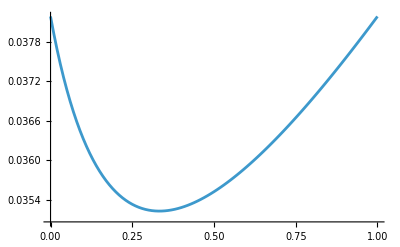

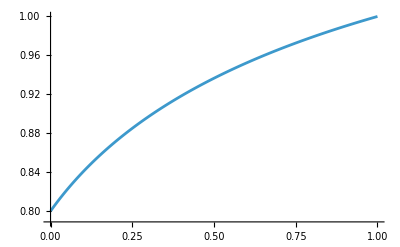

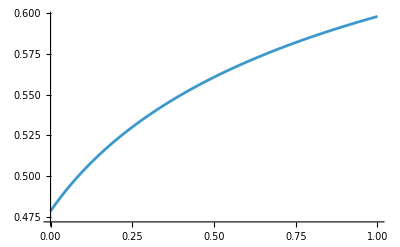

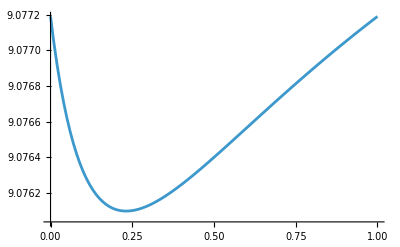

```mathematica
ListPlot[{highProportion,rho}/.table,Joined->True,PlotLegends->"rho"]
ListPlot[{highProportion,competitionMean}/.table,Joined->True,PlotLegends->"competition mean"]
ListPlot[{highProportion,SD}/.table,Joined->True,PlotLegends->"SD"]
ListPlot[{highProportion,sAveraged2[meanRichness/.x0Rule/.arrivalRate->1]}/.table,Joined->True,PlotLegends->"Richness"]
```

```mathematica
pInv[s_]=1-CDF[NormalDistribution[x0,SD]][0]/.x0Rule
```

1-1/2 Erfc[(-competitionMean+s)/(√2 SD)]

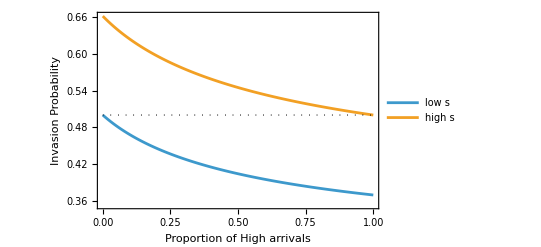

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
ListPlot[{{highProportion,pInv[lowS]}/.table,{highProportion,pInv[highS]}/.table},Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},PlotLegends->{"low s","high s"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Invasion Probability"}]
pInvLow=Interpolation[{highProportion,pInv[lowS]}/.table]
pInvHigh=Interpolation[{highProportion,pInv[highS]}/.table]
```

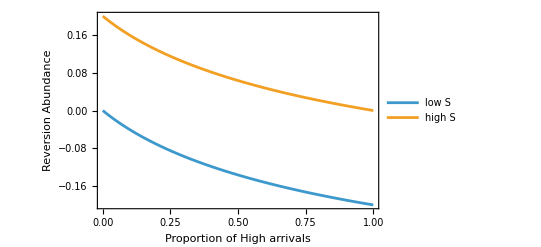

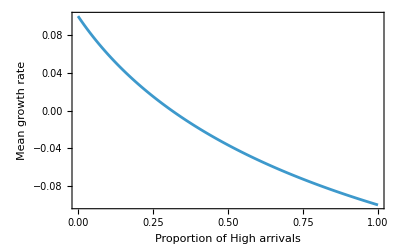

```mathematica
ListPlot[{{highProportion,s-competitionMean/.x0Rule/.s->lowS}/.table,{highProportion,s-competitionMean/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Reversion Abundance"}]
ListPlot[{highProportion,((s-competitionMean/.x0Rule/.s->lowS)+(s-competitionMean/.x0Rule/.s->highS))/2}/.table,Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean growth rate"}]
```

x0+(ⅇ^(-x0^2/(2 SD^2)) (√(2/π) SD+ⅇ^(x0^2/(2 SD^2)) x0+ⅇ^(x0^2/(2 SD^2)) x0 Erf[x0/(√2 SD)]))/(2 fastMFPT[x0/SD])

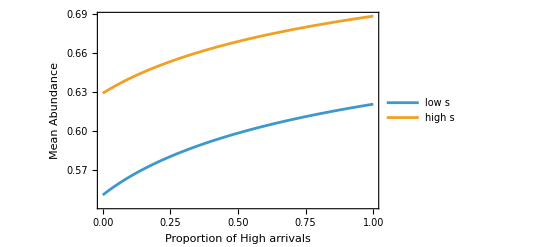

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
meanX
ListPlot[{{highProportion,meanX/.x0Rule/.s->lowS}/.table,{highProportion,meanX/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},PlotLegends->{"low s","high s"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean Abundance"}]
abundanceLow=Interpolation[{highProportion,meanX/.x0Rule/.s->lowS}/.table]
abundanceHigh=Interpolation[{highProportion,meanX/.x0Rule/.s->highS}/.table]
```

9.07719

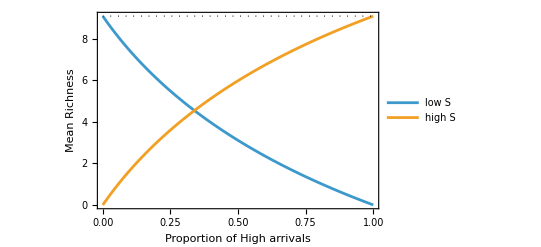

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
pureS = intVSFull/.x0Rule/.s->lowS/.table[[1]]
ListPlot[{{highProportion,(1-highProportion)*intVSFull/.x0Rule/.s->lowS}/.table,{highProportion,highProportion*intVSFull/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,pureS},{1,pureS}}]},PlotLegends->{"low S","high S"},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean Richness"}]
durationLow=Interpolation[{highProportion,(1-highProportion)*intVSFull/.x0Rule/.s->lowS}/.table]
durationHigh=Interpolation[{highProportion,highProportion*intVSFull/.x0Rule/.s->highS}/.table]
```

(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD+x0+x0 Erf[x0/(√2 SD)]+2 x0 fastMFPT[x0/SD])/(2 rho)

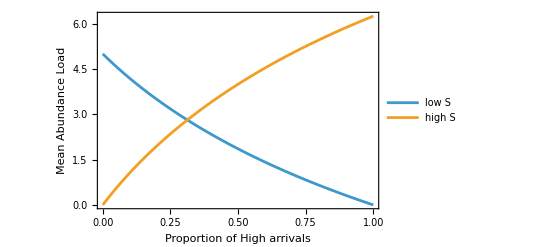

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
intMSFull
ListPlot[{{highProportion,(1-highProportion)*intMSFull/.x0Rule/.s->lowS}/.table,{highProportion,highProportion*intMSFull/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,pureS},{1,pureS}}]},PlotLegends->{"low S","high S"},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean Abundance Load"}]
loadLow=Interpolation[{highProportion,(1-highProportion)*intMSFull/.x0Rule/.s->lowS}/.table]
loadHigh=Interpolation[{highProportion,highProportion*intMSFull/.x0Rule/.s->highS}/.table]
```

```mathematica
(bExp=5/2/2)//N(*3/2*)
rRange=1
dDensity[r_]=(bExp-1)/(Pi*rRange^2)(1+(r/rRange)^2)^(-bExp)
Integrate[(bExp-1)/(Pi*rRange^2)(1+(r/rRange)^2)^(-bExp)*r*2*Pi,{r,0,Infinity}]
```

1.25

1

1/(4 π (1+r^2)^(5/4))

1

```mathematica
NX = NY =50
environment[{x_,y_}]:=HeavisideTheta[y-(NY/4)-1/4]+1
env=Table[environment[{1,y}],{y,1,NY}]
```

50

{1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

26

26

{0.152177,0.153449,0.076564,0.0450628,0.0298978,0.0214366,0.0161995,0.0127098,0.0102543,0.00845348,0.00708911,0.00602815,0.00518537,0.00450398,0.00394479,0.00348004,0.00308952,0.00275824,0.00247484,0.00223061,0.00201873,0.00183382,0.00167158,0.00152853,0.00140184,0.00128918,0.00140184,0.00152853,0.00167158,0.00183382,0.00201873,0.00223061,0.00247484,0.00275824,0.00308952,0.00348004,0.00394479,0.00450398,0.00518537,0.00602815,0.00708911,0.00845348,0.0102543,0.0127098,0.0161995,0.0214366,0.0298978,0.0450628,0.076564,0.153449}

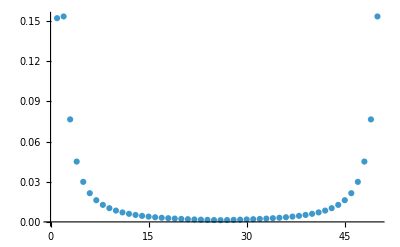

```mathematica
dKernelRaw=Table[dDensity[Sqrt[dx^2+dy^2]],{dy,-NY/2,NY/2-1},{dx,-NX/2,NX/2-1}]//N;
kernelCentreX=NX/2+1
kernelCentreY=NY/2+1
dKernelRaw[[kernelCentreX,kernelCentreY]]=0;
dKernelRaw=dKernelRaw/Total[dKernelRaw,2];
yKernel=RotateRight[Total[dKernelRaw,{2}],NY/2]
yKernelTransform=Sqrt[NY]*Fourier[yKernel];
ListPlot[yKernel,PlotRange->All]
```

```mathematica
abundance1=loadHigh[1](2-env);
abundance2=loadHigh[1](env-1);
highProp=Table[1/2,NY];
oneProp=(2-env);
stepsPerInvasionAttempt=15/3; (* / 10 *)
bodyMass = 10^-4;
dispersalRate = bodyMass * 10^(-3);
offspringDispersalRate = dispersalRate/bodyMass;
```

```mathematica
(* We measure all rates in units of offspringDispersalRate! *)
For[ii=1,ii<1000,ii++,incoming1=InverseFourier[Fourier[abundance1]*yKernelTransform]//Chop;
incoming2=InverseFourier[Fourier[abundance2]*yKernelTransform]//Chop;
incoming1=incoming1+1/(NX*NY)/stepsPerInvasionAttempt/offspringDispersalRate;
incoming2=incoming2+1/(NX*NY)/stepsPerInvasionAttempt/offspringDispersalRate;
incoming=incoming1+incoming2;
oneProp=incoming1/incoming;
abundance1=MapThread[#1[[#2]]&,{{loadHigh[oneProp],loadLow[1-oneProp]}//Transpose,env}];
abundance2=MapThread[#1[[#2]]&,{{loadLow[oneProp],loadHigh[1-oneProp]}//Transpose,env}];
]
```

```mathematica
theoryBiomass=ListPlot[{abundance1,abundance2},PlotRange->{0,Automatic},PlotLegends->{"Biomass 1 (theory)", "Biomass 2 (theory)"},PlotMarkers->"□"];
biomassSim=Import["biomass_by_type.csv", HeaderLines->{1,1}]//Transpose;
simlationBiomass=ListPlot[{biomassSim[[1]],biomassSim[[2]]}//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Biomass 1 (sim)", "Biomass 2 (sim)"},
PlotMarkers->"●"];
Show[theoryBiomass,simlationBiomass,PlotRange->All]
```

-Graphics-

```mathematica
(* Using this solution, now compute species-level dispersal parameter: *)pInv1=MapThread[#1[[#2]]&,{{pInvHigh[oneProp],pInvLow[1-oneProp]}//Transpose,env}]
pInv2=MapThread[#1[[#2]]&,{{pInvLow[oneProp],pInvHigh[1-oneProp]}//Transpose,env}]
alpha1=MapThread[#1[[#2]]&,{{durationHigh[oneProp],durationLow[1-oneProp]}//Transpose,env}]
alpha2=MapThread[#1[[#2]]&,{{durationLow[oneProp],durationHigh[1-oneProp]}//Transpose,env}]
meanAbundance1=abundance1/alpha1
meanAbundance2=abundance2/alpha2
rExt1=incoming1*pInv1/alpha1
rExt2=incoming2*pInv2/alpha2
(* in units of propagule attivals *)
```

{0.553104,0.541687,0.535365,0.53165,0.529527,0.528553,0.528553,0.529527,0.53165,0.535365,0.541687,0.553104,0.390755,0.384582,0.381125,0.378917,0.377383,0.376255,0.375394,0.374717,0.374174,0.373731,0.373365,0.373061,0.372808,0.372597,0.372428,0.372297,0.372201,0.372138,0.372107,0.372107,0.372138,0.372201,0.372297,0.372428,0.372597,0.372808,0.373061,0.373365,0.373731,0.374174,0.374717,0.375394,0.376255,0.377383,0.378917,0.381125,0.384582,0.390755}

{0.410158,0.401195,0.396263,0.393374,0.391727,0.390973,0.390973,0.391727,0.393374,0.396263,0.401195,0.410158,0.528272,0.520283,0.515789,0.512913,0.510911,0.509439,0.508313,0.507428,0.506717,0.506137,0.505658,0.50526,0.504927,0.504652,0.50443,0.504258,0.504132,0.504049,0.504008,0.504008,0.504049,0.504132,0.504258,0.50443,0.504652,0.504927,0.50526,0.505658,0.506137,0.506717,0.507428,0.508313,0.509439,0.510911,0.512913,0.515789,0.520283,0.528272}

{5.47441,6.18571,6.59351,6.838,6.97931,7.04454,7.04454,6.97931,6.838,6.59351,6.18571,5.47441,2.01327,1.46783,1.15316,0.948706,0.804956,0.69846,0.616603,0.551962,0.499868,0.457243,0.42198,0.392604,0.368073,0.347673,0.331258,0.318504,0.309152,0.303018,0.29998,0.29998,0.303018,0.309152,0.318504,0.331258,0.347673,0.368073,0.392604,0.42198,0.457243,0.499868,0.551962,0.616603,0.69846,0.804956,0.948706,1.15316,1.46783,2.01327}

{3.6019,2.89074,2.48303,2.23859,2.09732,2.0321,2.0321,2.09732,2.23859,2.48303,2.89074,3.6019,7.06338,7.60895,7.92371,8.12822,8.27201,8.37853,8.46041,8.52507,8.57718,8.61982,8.65509,8.68447,8.70901,8.72942,8.74584,8.7586,8.76795,8.77409,8.77712,8.77712,8.77409,8.76795,8.7586,8.74584,8.72942,8.70901,8.68447,8.65509,8.61982,8.57718,8.52507,8.46041,8.37853,8.27201,8.12822,7.92371,7.60895,7.06338}

{0.665805,0.670367,0.672965,0.674517,0.675412,0.675825,0.675825,0.675412,0.674517,0.672965,0.670367,0.665805,0.60647,0.610397,0.612645,0.614099,0.615118,0.615872,0.61645,0.616906,0.617273,0.617573,0.617821,0.618028,0.6182,0.618344,0.618459,0.618548,0.618614,0.618657,0.618679,0.618679,0.618657,0.618614,0.618548,0.618459,0.618344,0.6182,0.618028,0.617821,0.617573,0.617273,0.616906,0.61645,0.615872,0.615118,0.614099,0.612645,0.610397,0.60647}

{0.594791,0.600065,0.603055,0.604836,0.605861,0.606333,0.606333,0.605861,0.604836,0.603055,0.600065,0.594791,0.675944,0.679383,0.681358,0.682637,0.683535,0.6842,0.68471,0.685112,0.685437,0.685702,0.685921,0.686104,0.686256,0.686383,0.686485,0.686564,0.686622,0.68666,0.686679,0.686679,0.68666,0.686622,0.686564,0.686485,0.686383,0.686256,0.686104,0.685921,0.685702,0.685437,0.685112,0.68471,0.6842,0.683535,0.682637,0.681358,0.679383,0.675944}

{0.272963,0.282628,0.289373,0.293874,0.296635,0.297948,0.297948,0.296635,0.293874,0.289373,0.282628,0.272963,0.421106,0.435495,0.444988,0.451675,0.456634,0.460448,0.463463,0.465895,0.467889,0.469543,0.470925,0.472085,0.473058,0.473869,0.474522,0.47503,0.475402,0.475647,0.475768,0.475768,0.475647,0.475402,0.47503,0.474522,0.473869,0.473058,0.472085,0.470925,0.469543,0.467889,0.465895,0.463463,0.460448,0.456634,0.451675,0.444988,0.435495,0.421106}

{0.391336,0.401966,0.409762,0.415076,0.418367,0.41994,0.41994,0.418367,0.415076,0.409762,0.401966,0.391336,0.298833,0.310723,0.318458,0.323867,0.32786,0.330924,0.33334,0.335287,0.336881,0.338201,0.339304,0.34023,0.341007,0.341654,0.342175,0.34258,0.342877,0.343072,0.343169,0.343169,0.343072,0.342877,0.34258,0.342175,0.341654,0.341007,0.34023,0.339304,0.338201,0.336881,0.335287,0.33334,0.330924,0.32786,0.323867,0.318458,0.310723,0.298833}

```mathematica
Export["metacommunity_fields.csv",Join[{{"pColonisation1","pColonisation2","meanAbundance1","meanAbundance2","extirpationRate1","extirpationRate2"}},Transpose[{pInv1,pInv2,meanAbundance1,meanAbundance2,rExt1,rExt2}]]]
```

metacommunity_fields.csv

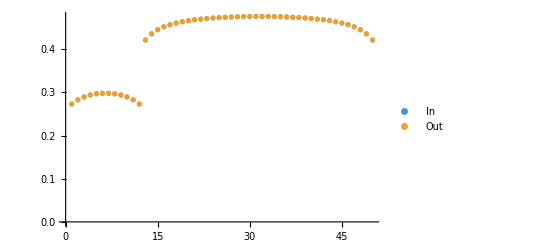

```mathematica
ListPlot[{incoming1*pInv1/alpha1,incoming1*pInv1/alpha1},PlotLegends->{"In","Out"},PlotRange->{0,All}]
```

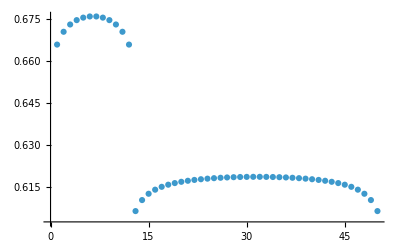

```mathematica
ListPlot[meanAbundance1]
```

```mathematica
densityX1=Table[1,{NY}]
dt=0.01;
ii=.
PrintTemporary@Dynamic@{Clock@Infinity,decayRate1};
For[ii=1,ii<100000,ii++,
lastTotalX1=Total[densityX1];
abundanceX1=(densityX1/alpha1)*MapThread[#1[[#2]]&,{{loadHigh[oneProp],loadLow[1-oneProp]}//Transpose,env}];
incomingX1=InverseFourier[Fourier[abundanceX1]*yKernelTransform]//Chop;
colonisationX1=incomingX1*pInv1;
densityX1+=(colonisationX1 - densityX1*rExt1)*dt;
decayRate1=Log[Total[densityX1]/lastTotalX1]/dt
]
decayRate1
1/(stepsPerInvasionAttempt*Abs[decayRate1])
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

-0.00767993

26.0419

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

0.391336

-0.00503136

39.7506

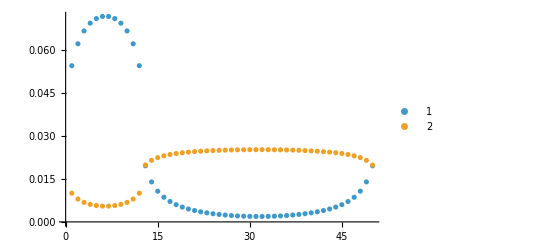

```mathematica
densityX2=Table[1,{NY}]
dt=0.01;
ii=.
Print[rExt2[[1]]]
PrintTemporary@Dynamic@{Clock@Infinity,decayRate2};
For[ii=1,ii<100000,ii++,
lastTotalX2=Total[densityX2];
abundanceX2=(densityX2/alpha2)*MapThread[#1[[#2]]&,{{loadLow[oneProp],loadHigh[1-oneProp]}//Transpose,env}];
incomingX2=InverseFourier[Fourier[abundanceX2]*yKernelTransform]//Chop;
colonisationX2=incomingX2*pInv2;
densityX2+=(colonisationX2 - densityX2*rExt2)*dt;
decayRate2=Log[Total[densityX2]/lastTotalX2]/dt
]
decayRate2
1/(stepsPerInvasionAttempt*Abs[decayRate2])
ListPlot[{densityX1/Total[densityX1],densityX2/Total[densityX2]},PlotRange->{0,Automatic},PlotLegends->{1,2}]
```

```mathematica
richnessSim=Import["richness_by_type.csv", HeaderLines->{1,1}]//Transpose;
simlationRichness=ListPlot[{richnessSim[[1]],richnessSim[[2]],Total[richnessSim,{1}]}//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Mean Richness 1 (LVMCM-PSD)", "Mean Richness 2 (LVMCM-PSD)","Mean Combined Richness "},
PlotMarkers->"●",Frame->True,FrameLabel->{"Row", "Richness"}];
theoryRichness=ListPlot[{alpha1,alpha2,alpha1+alpha2}*2.4//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Mean Richness 1 (Type-Based)", "Mean Richness 2 (Type-Based)","Mean Combined Richness "},
PlotMarkers->"□",Frame->True,FrameLabel->{"Row", "Richness"}];
Show[theoryRichness,simlationRichness,PlotRange->All]
```

-Graphics-

```mathematica
richnessCDFTP=Import["richness_by_type_dcftp.csv", HeaderLines->{1,1}]//Transpose;
CDFTPRichness=ListPlot[{richnessCDFTP[[1]],richnessCDFTP[[2]],richnessCDFTP[[1]]+richnessCDFTP[[2]]}//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Mean Richness 1 (CDFTP)", "Mean Richness 2 (CDFTP)","Mean Combined Richness "},
PlotMarkers->"●",Frame->True,FrameLabel->{"Row", "Richness"}];
Show[CDFTPRichness,PlotRange->All]
```

-Graphics-

```mathematica
rarityCDFTP=Import["range_rarity_dcftp.csv", HeaderLines->{1,1}]//Transpose;
raritySim=Import["range_rarity.csv", HeaderLines->{1,1}]//Transpose;
rarityPlot=ListPlot[{raritySim[[1]],rarityCDFTP[[1]]}//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"LVMCM-PSD", "CDFTP","Mean Combined Richness "},
PlotMarkers->"●",Frame->TrueFrameLabel->{"Row", "Range Size Rarity"}];
Show[rarityPlot,PlotRange->All]
```

-Graphics-

```mathematica
SetDirectory["/Users/btw970/lin_alg/ambition/The-Lotka-Volterra-Metacommunity-Model/Infinite_pool_assembly"]
```

/Users/btw970/lin_alg/ambition/The-Lotka-Volterra-Metacommunity-Model/Infinite_pool_assembly